```mathematica
SetDirectory[NotebookDirectory[]];
case=4;
Switch[case,
1,T=50;filename="Fig4a.png";,
2,T=10;filename="Fig4b.png";,
3,T=5;filename="Fig4c.png";,
4,T=2;filename="Fig4d.png";
]
C0=0.5;C1=1;τ1=0.15;τ2=0.2;τ3=0.8;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=200;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];
(*Look for equilibrium original system*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
(*equilibrium averaged*)
A1 = 1/T Integrate[1/Ct[t],{t,0,T}];
A3= 1/T Integrate[1/Ct[t]^3,{t,0,T}];
eqn2=FindRoot[0==v-(A3/A1^3) v^3/3-(v+β)/γ,{v,-1}];
{v00,w00}={v,(v+β)/γ}/.eqn2;
```

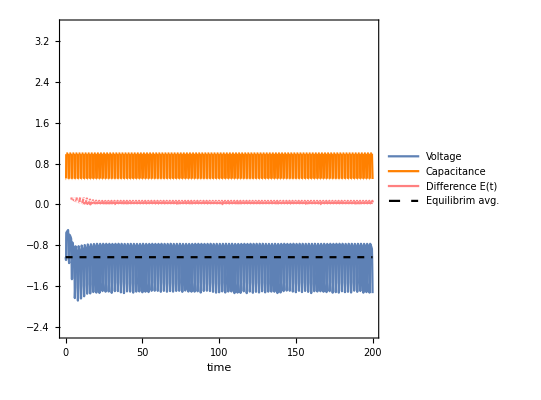

Fig4d.png

```mathematica
(*Simulation*)
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v00,w[0]==w00},{v,w},{t,0,maxtime},MaxStepSize->0.01];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,3.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{None,None},{"time",None}},
LabelStyle->Directive[Black,FontSize->16]
];
(*PlotLegends->Placed[StringJoin["C0=",ToString[C0],", C1=",ToString[C1],", T= ",ToString[T],",\n","τ1= ",ToString[τ1],", τ2= ",ToString[τ2],", τ3= ",ToString[τ3],",\n","ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above],ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],
ColorFunctionScaling->False,*)
capacitance=Plot[{Ct[t]},{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];
equilibrium2= Plot[v00,{t,0,maxtime},
PlotStyle->{Black,Dashed}];
error = Plot[Max[Abs[Ct[t] V[t]-(1/A1)v00],Abs[W[t]-w00]],{t,0,maxtime},PlotStyle->Pink];
g1=Legended[Show[voltage, capacitance,equilibrium2,error,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange,Pink,Directive[Black,Dashed]},{Style["Voltage",FontSize->14],Style["Capacitance",FontSize->14],Style["Difference E(t)",FontSize->14],Style["Equilibrim avg.",FontSize->14]},LegendLayout->"Row"],{{0.5,0.92}}]]
Export[filename,g1]
```